```mathematica
Λ = 75 10^-9; (*Unit: meter*)
ωp = 6.18;      (* unit: eV *)
γ = 20 10^-3; (* unit: eV *)
ϵ[ω_] := 1 - ωp^2/(ω (ω + I γ));
```

```mathematica
α[ω_] := (ϵ[ω]-1)/(ϵ[ω]+2);        (* unit: 4 Subscript[πϵ, 0] a^3 *)
a = 25 10^-9; (*Unit: meter*)
ω0 = (3 10^8 6.62 10^-34)/(Λ 1.6 10^-19) ;  (* c/Λ, unit: eV*)
```

```mathematica
Problem 1
```

Integrate::idiv: -(12.7308 Re[1/(12.7308-(0.+0.02 ⅈ) ν-1. ν^2)])/(0.+ν) 的积分在 {-20,-0.005} 上不收敛.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {ν} = {-3.55911} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.58212+0. ⅈ 和 0.00720677.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {ν} = {3.59754} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -6.58212+0. ⅈ 和 0.00720677.

NIntegrate::ncvb: 在接近 {ν} = {-3.55243} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 6.59863+0. ⅈ 和 0.0144314.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

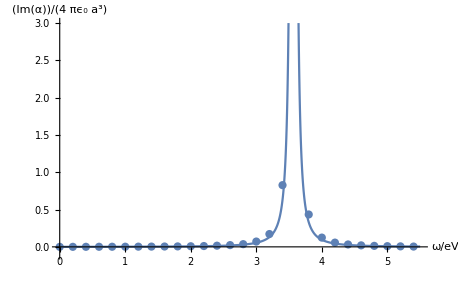

```mathematica
o = 0.005; L = 20;
Show[Show[Plot[Im[α[ω]], {ω, 0, 5.5}, PlotRange->{-0.1, 3}],AxesLabel->{HoldForm[ω/eV],HoldForm[Im[α]/(4 Subscript[πϵ, 0] a^3)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}],
ListPlot[Table[{ω, 1/π N[∫_-L^(ω-o) Re[α[ν]]/(ω - ν)ⅆν + ∫_(ω+o)^L Re[α[ν]]/(ω - ν)ⅆν]}, {ω, 0, 5.5, 0.2}]]]
```

NIntegrate::ncvb: 在接近 {ν} = {-3.52461} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.57077+0. ⅈ 和 0.00609507.

NIntegrate::ncvb: 在接近 {ν} = {3.57264} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.57077+0. ⅈ 和 0.00609507.

NIntegrate::ncvb: 在接近 {ν} = {-3.56317} 处的 ν 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.44695+0. ⅈ 和 0.0054381.

General::stop: 在本次计算中，NIntegrate::ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

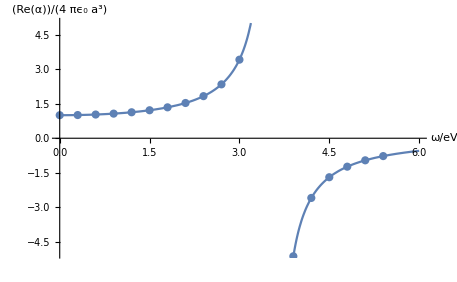

```mathematica
o = 0.01; L = 25;
Show[Show[Plot[Re[α[ω]], {ω, 0, 6}, PlotRange->{-5, 5}],AxesLabel->{HoldForm[ω/eV],HoldForm[Re[α]/(4 Subscript[πϵ, 0] a^3)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}],
ListPlot[Table[{ω,- 1/π N[∫_-L^(ω-o) Im[α[ν]]/(ω - ν)ⅆν + ∫_(ω+o)^L Im[α[ν]]/(ω - ν)ⅆν]}, {ω, 0, 5.5, 0.3}]]]
```

Problem 3

```mathematica
αxy[ω_, k_] := N[α[ω]/(1- α[ω](a/Λ)^3((ω/ω0)^2 (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) + ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) - (PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) ))];
 (*unit: ω eV, k  π/Λ*)
```

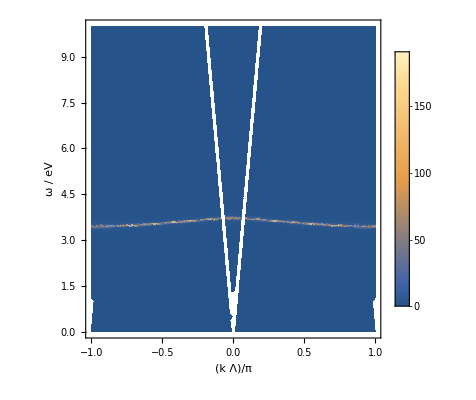

```mathematica
DensityPlot[Im[αxy[ω,k]], {k, -1, 1}, {ω, 0, 10}, PlotPoints->100,PlotLegends->Automatic,PlotRange->All,FrameLabel->{"(k Λ)/π", "ω / eV"}]
```

```mathematica
αz[ω_, k_] := N[α[ω]/(1- α[ω](a/Λ)^3(-2ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) +2(PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) ))];
 (*unit: ω eV, k  π/Λ*)
```

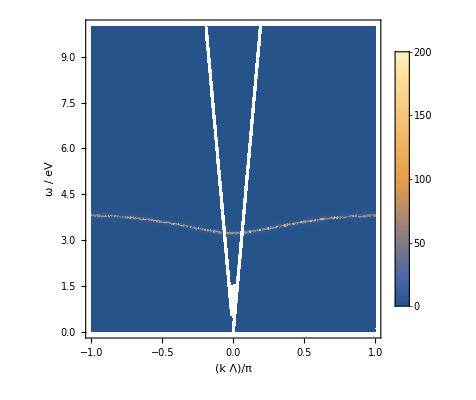

```mathematica
DensityPlot[Im[αz[ω,k]], {k, -1, 1}, {ω, 0, 10}, PlotPoints->100,PlotLegends->Automatic,PlotRange->All,FrameLabel->{"(k Λ)/π", "ω / eV"}]
```

Problem 4

```mathematica
ωxy[k_] := ωp N[√(1/3(1 + (a/Λ)^3 (PolyLog[3, ⅇ^(ⅈ π k)] + PolyLog[3, ⅇ^(-ⅈ π k)])))]; (*unit of k: π / Λ, output unit: eV*)
```

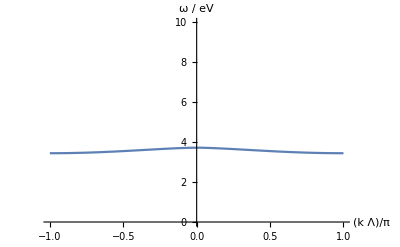

```mathematica
Plot[ωxy[k], {k, -1, 1}, PlotRange->{0, 10}, AxesLabel->{"(k Λ)/π", "ω / eV"}]
```

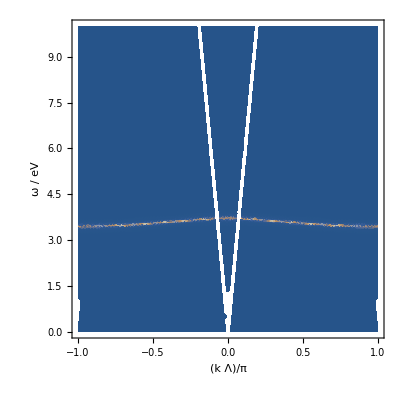
```mathematica
Show[-Graphics-,Plot[ωxy[k], {k, -1, 1}, PlotRange->{0, 10}, AxesLabel->{"(k Λ)/π", "ω / eV"},PlotStyle->Yellow]]
```

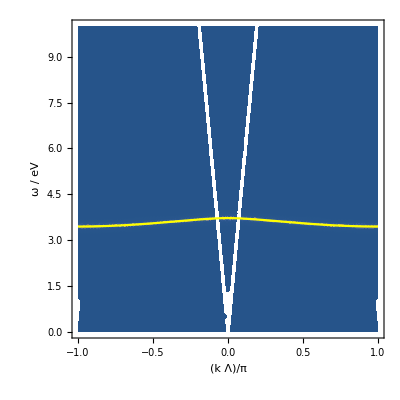

```mathematica
ωz[k_] := ωp N[√(1/3(1 -2 (a/Λ)^3(PolyLog[3, ⅇ^(ⅈ π k)] + PolyLog[3, ⅇ^(-ⅈ π k)])))]; (*unit of k: 1 / Λ, output unit: eV*)
```

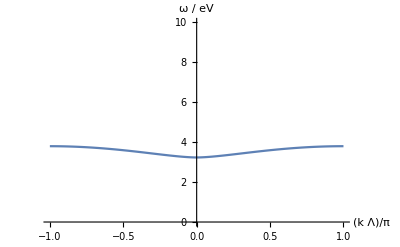

```mathematica
Plot[ωz[k], {k, -1, 1}, PlotRange->{0, 10}, AxesLabel->{"(k Λ)/π", "ω / eV"}]
```

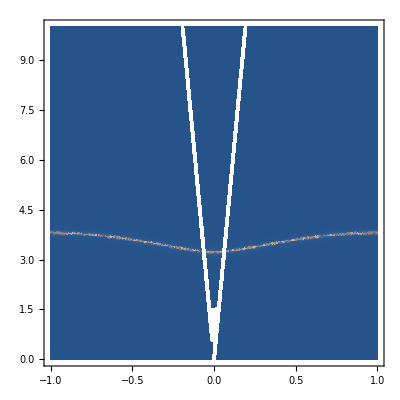
```mathematica
Show[-Graphics-,Plot[ωz[k], {k, -1, 1}, PlotRange->{0, 10}, AxesLabel->{"(k Λ)/π", "ω / eV"}, PlotStyle->Yellow]]
```

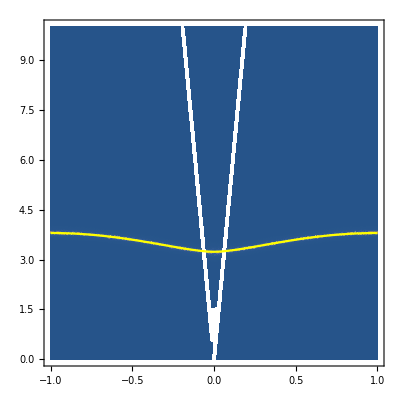

Tests about the V-shape blank area.

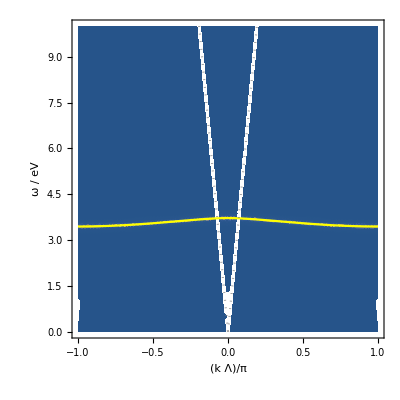

```mathematica
Show[-Graphics-,Plot[{π ω0 k, -π ω0 k}, {k, -1, 1}, PlotRange->{0, 10}, AxesLabel->{"(k Λ)/π", "ω / eV"}, PlotStyle->{{Gray, Dotted}, {Gray, Dotted}}]]
```

```mathematica
Show[-Graphics-,Plot[{π ω0 k, -π ω0 k}, {k, -1, 1}, PlotRange->{0, 10}, AxesLabel->{"(k Λ)/π", "ω / eV"}, PlotStyle->{{Gray, Dotted}, {Gray, Dotted}}]]
```

-Graphics-

```mathematica
Show[-Graphics-,AxesLabel->{None,None},FrameLabel->{{HoldForm["ω / eV"],None},{HoldForm["(k Λ)/π"],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-